## Brown

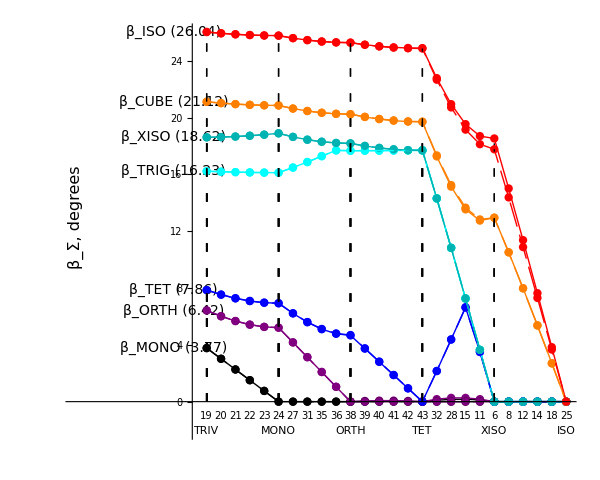

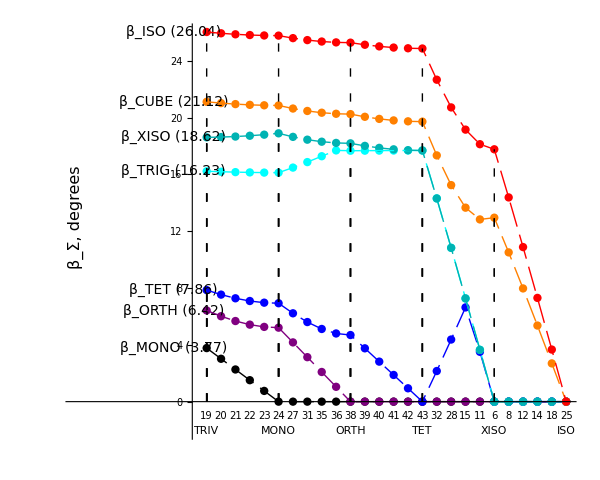

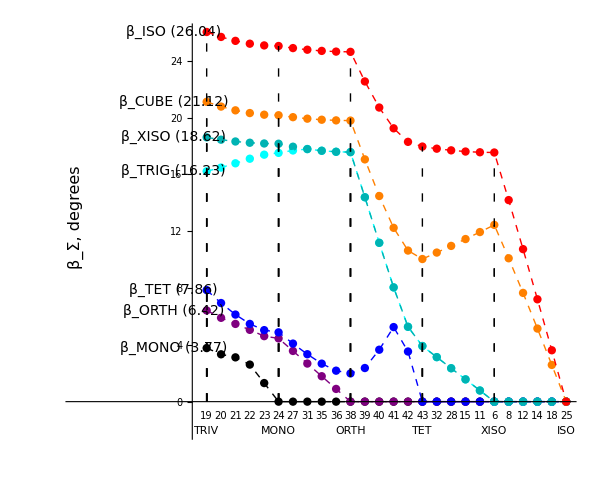

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

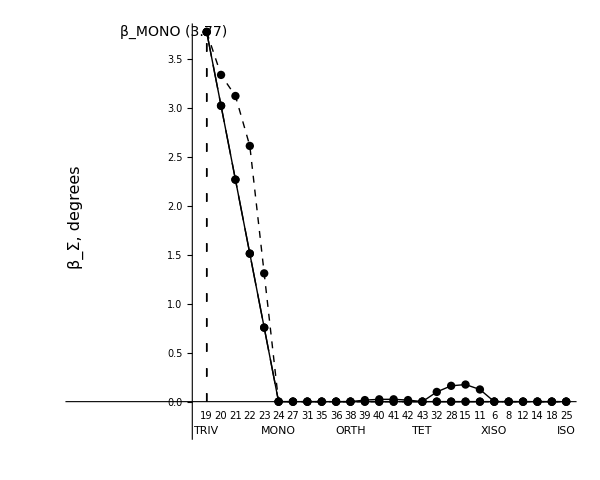
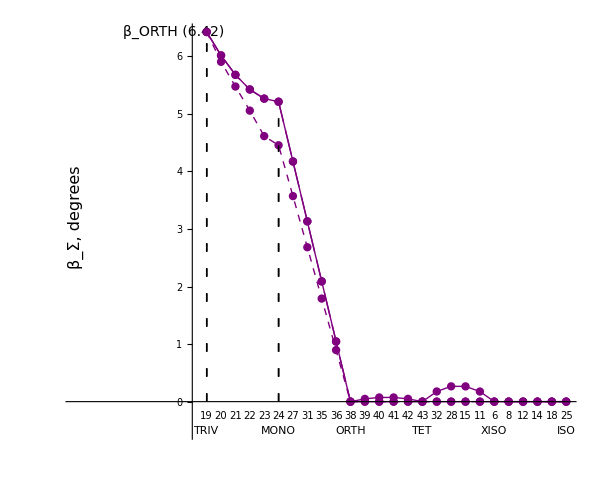
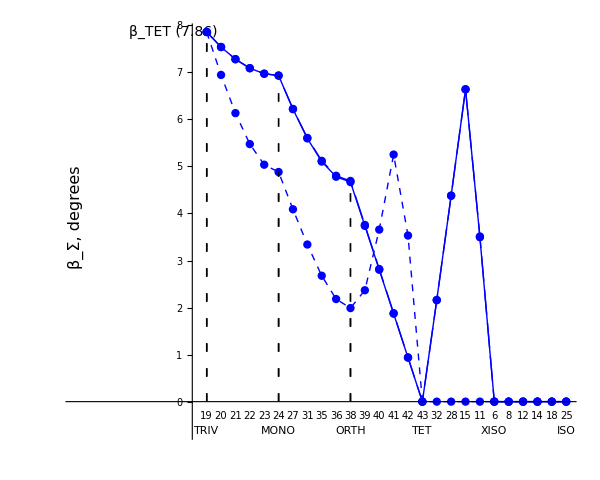
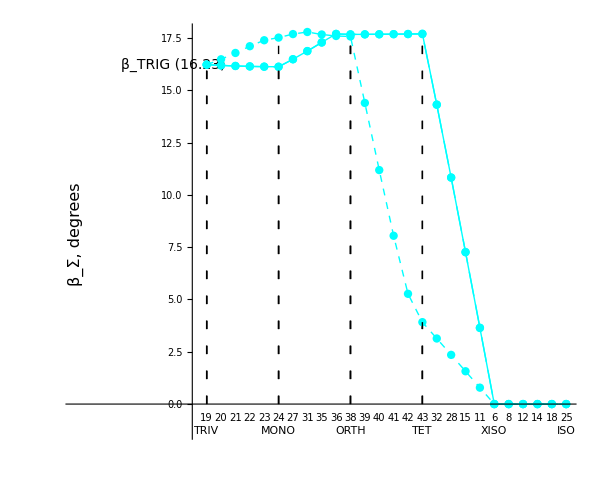
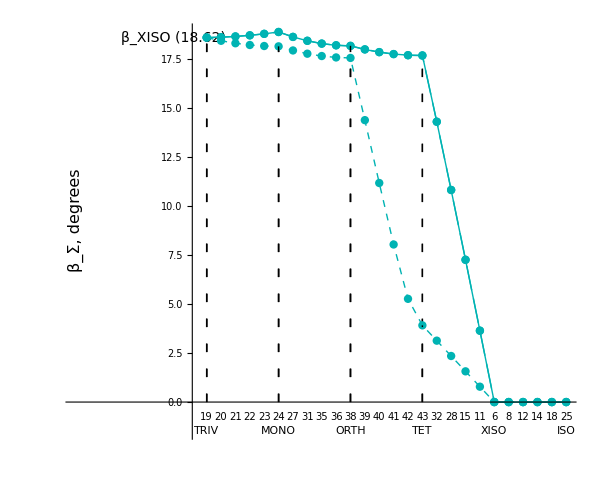
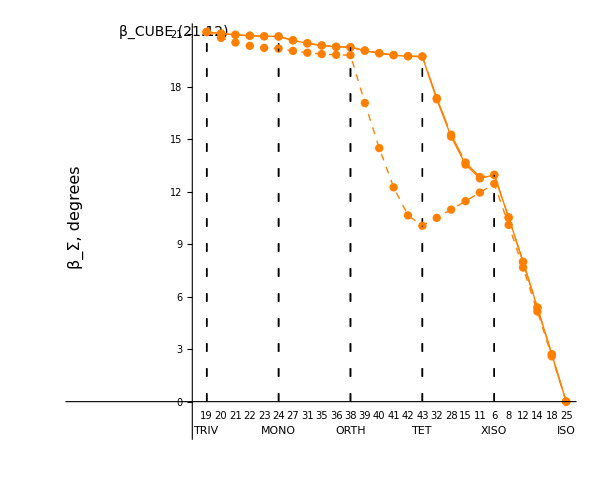
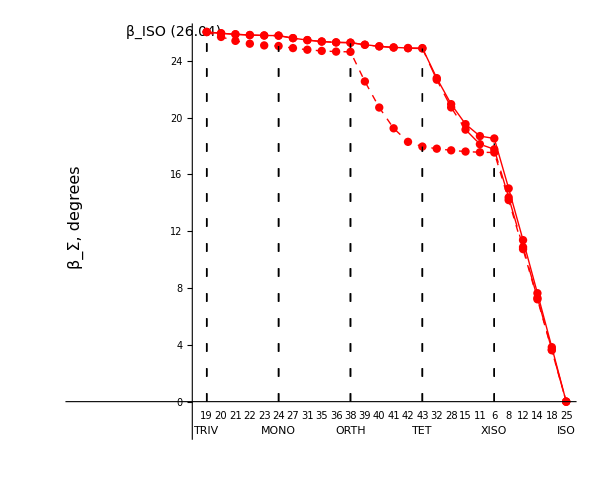

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ
```

#### nm2 and nm3 (these may be very similar)

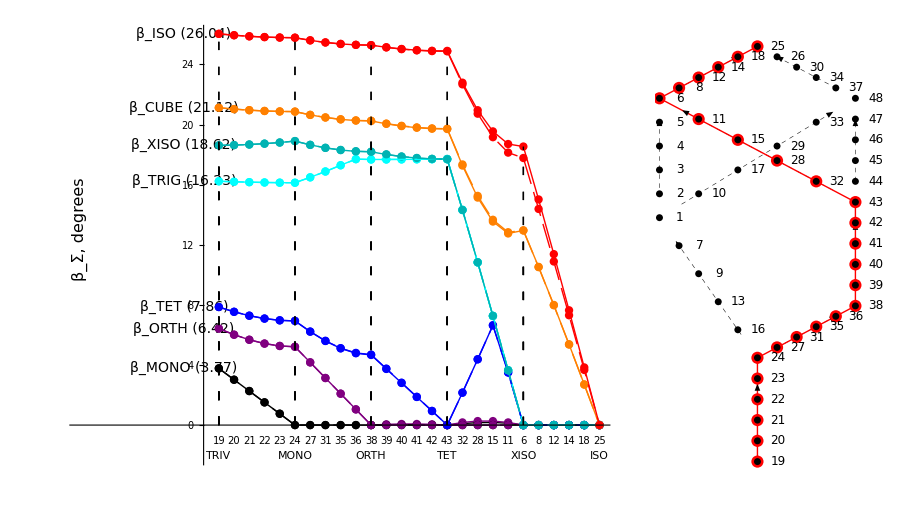

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnXISO,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,ΣnXISO]},ImageSize->900,Spacings->0]
```

#### Three node sequences for nm2 and nm4 (based on AllPoints)

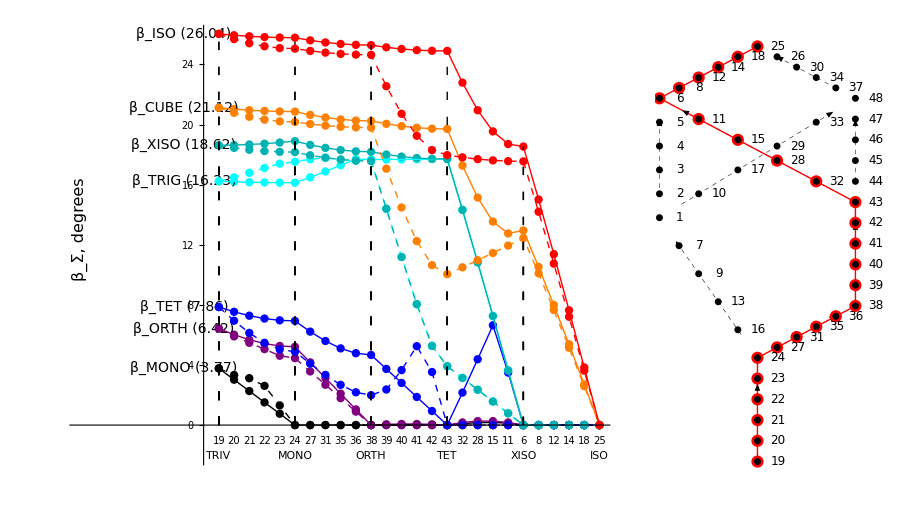

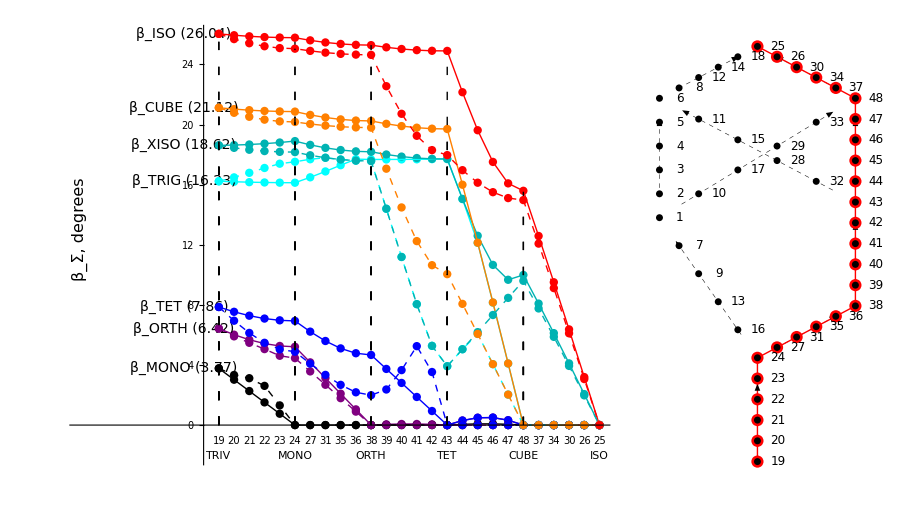

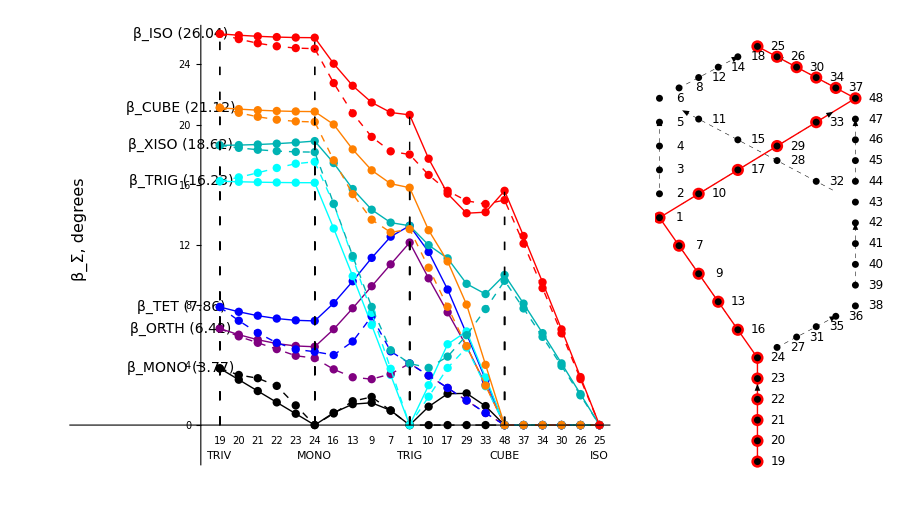

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnXISO,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnXISO]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnCUBE,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnCUBE]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTRIG,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTRIG]},ImageSize->900,Spacings->0]
```

#### Compare beta curves for nm2 and nm3 (These plots do not have the whistles and bells of the plots above.)

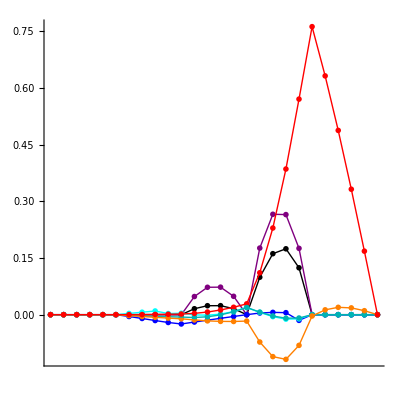

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

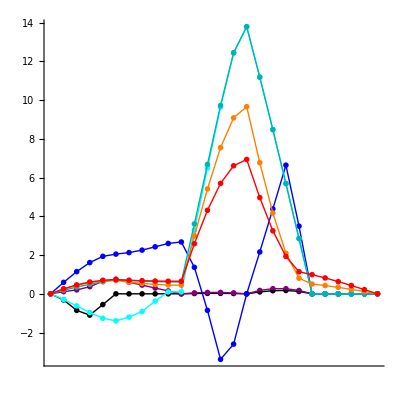

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```